## Hexi—PS7—2025-02-10

### Exercises from EIWL3 Section 20

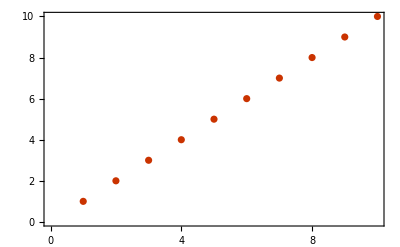

```mathematica
ListPlot[Range[10],PlotTheme->"Web"]
```

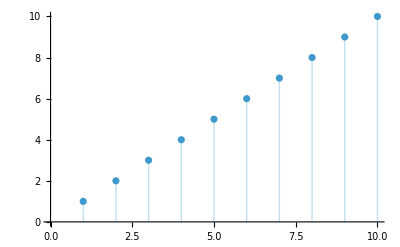

```mathematica
ListPlot[Range[10],Filling->Axis]
```

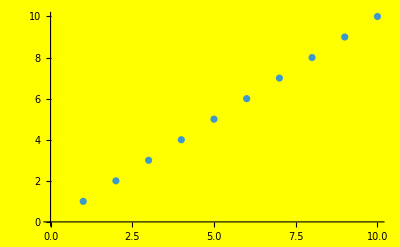

```mathematica
ListPlot[Range[10],Background->Yellow]
```

```mathematica
GeoListPlot[Entity["Country","Australia"],GeoRange->Entity["Planet","Earth"]]
```

-Graphics-

```mathematica
GeoListPlot[Entity["Country","Madagascar"],GeoRange->Entity["Ocean","IndianOcean"]]
```

-Graphics-

```mathematica
GeoListPlot[EntityClass["Country","SouthAmerica"],GeoBackground->"ReliefMap"]
```

-Graphics-

```mathematica
GeoListPlot[{Entity["Country","France"],Entity["Country","Finland"],Entity["Country","Greece"]},GeoRange->Entity["GeographicRegion","Europe"],GeoLabels->Automatic]
```

-Graphics-

```mathematica
GeoListPlot[EntityClass["University","TheIvyLeague"],GeoLabels->True]
```

-Graphics-

```mathematica
Grid[Table[i*j,{i,12},{j,12}],ItemStyle->White,Background->Black]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Table[Graphics[Disk[],ImageSize->RandomInteger[40]],100]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[RegularPolygon[5],ImageSize->30,AspectRatio->n],{n,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[Graphics[Circle[],ImageSize->n],{n,5,500}]
```

```mathematica
Grid[Table[RandomColor[],{10},{10}],Frame->All]
```

RGBColor[0.05498036276444207, 0.7330405533063669, 0.3986152085283383] | RGBColor[0.29797006583703634, 0.35430478797125264, 0.0450917699511979] | RGBColor[0.6339757182537229, 0.8623973128910807, 0.9658168695879421] | RGBColor[0.22181202608734263, 0.5270073754452467, 0.5228994322266407] | RGBColor[0.7284881674010302, 0.30559157738626785, 0.6479432298478913] | RGBColor[0.09553118814885653, 0.0331361598531934, 0.557264920850004] | RGBColor[0.21757269535601642, 0.8442093169297076, 0.53006410406722] | RGBColor[0.7821001590548258, 0.702742056368117, 0.04533869239673738] | RGBColor[0.964612811637054, 0.577839704585323, 0.9850854840657728] | RGBColor[0.8447738171971144, 0.5095865649758666, 0.15287021667291678]
RGBColor[0.5220200851158414, 0.4950130194954929, 0.6782469858533644] | RGBColor[0.15035579260412724, 0.9503502500905152, 0.45951424898796334] | RGBColor[0.6190527938411556, 0.19535131375869264, 0.8944955219962061] | RGBColor[0.10884506825718887, 0.667915612742398, 0.47913707535201744] | RGBColor[0.6250023738997199, 0.516619513671478, 0.2502776852103663] | RGBColor[0.9040490522052367, 0.7670448219664665, 0.5457082403363271] | RGBColor[0.46624766096168857, 0.22351859654502748, 0.7003832502213343] | RGBColor[0.842747337384725, 0.9285644382292284, 0.9563522763779586] | RGBColor[0.4203724356681411, 0.23239395059313028, 0.7892450482679183] | RGBColor[0.8765992845703312, 0.1510399107400071, 0.4936992566174885]
RGBColor[0.2307396535591646, 0.4351551595435168, 0.9361579572613319] | RGBColor[0.9485289685640041, 0.8310146526605275, 0.18841015638923286] | RGBColor[0.2513193657509476, 0.6976359384801025, 0.12755069792494012] | RGBColor[0.6857725480880843, 0.9394740100571648, 0.8327998510871872] | RGBColor[0.598396642505427, 0.47455291984588843, 0.4109913181423581] | RGBColor[0.6558821426744819, 0.5785562926459824, 0.5990154131522352] | RGBColor[0.3004550295989685, 0.9251691147903323, 0.5873988118678843] | RGBColor[0.6842518674217639, 0.8166938747770145, 0.4169706080479525] | RGBColor[0.3969287776619248, 0.3599597941136974, 0.2701307354099347] | RGBColor[0.1413537429825389, 0.22867541260128244, 0.9261352381264147]
RGBColor[0.9276796101353018, 0.8761018376628014, 0.7166955701418736] | RGBColor[0.7059230503942344, 0.06247318805917046, 0.8341228935027976] | RGBColor[0.06629249922776692, 0.4719077170536454, 0.3223763566243232] | RGBColor[0.3641932255657707, 0.04615731707592019, 0.09123205397277534] | RGBColor[0.4234897423669364, 0.73287912385458, 0.7337792101059444] | RGBColor[0.5454270932280996, 0.7719802807805136, 0.4648892085215526] | RGBColor[0.9513106323796297, 0.5001858218924728, 0.14950117174028899] | RGBColor[0.2252854487753373, 0.7838855579516748, 0.8206565263547168] | RGBColor[0.9991707533123924, 0.585694978219673, 0.9511839894312231] | RGBColor[0.9067608418546358, 0.09272738956740523, 0.24587924193108734]
RGBColor[0.8716987159887508, 0.29384654607949034, 0.04895099134267533] | RGBColor[0.21997855582549564, 0.18921361095203593, 0.9478471939346735] | RGBColor[0.9314869731884685, 0.7598285117548513, 0.9320783030204525] | RGBColor[0.7991810003552038, 0.9445099335462896, 0.9875475130258016] | RGBColor[0.42194449221385577, 0.5598752795852373, 0.570124074254158] | RGBColor[0.7019696849466155, 0.33891828532262047, 0.16197982726683002] | RGBColor[0.9604658981448326, 0.9764421554510081, 0.023389942272614928] | RGBColor[0.7298306457395505, 0.1854664151583323, 0.7155670992478045] | RGBColor[0.5244365579436547, 0.5675705323795872, 0.013739443659239736] | RGBColor[0.48116765586852206, 0.6132900918947775, 0.575455902813885]
RGBColor[0.5661760088381764, 0.7508651823027321, 0.8463616102140792] | RGBColor[0.6951901769096336, 0.38410527327620136, 0.21720864828502395] | RGBColor[0.41283922207403, 0.9505577955450788, 0.9727631555156868] | RGBColor[0.22249245446465205, 0.9020569939497145, 0.2889786914522281] | RGBColor[0.5287442391080168, 0.2391585197328543, 0.7639106866177827] | RGBColor[0.40543328385157396, 0.4046316260272622, 0.33231450873012247] | RGBColor[0.684279564431648, 0.12950459241139733, 0.16087644868839446] | RGBColor[0.09056302384855819, 0.6794475562453097, 0.20816113444808937] | RGBColor[0.6760264338954218, 0.05581079488585794, 0.6574570790162739] | RGBColor[0.4448798034323427, 0.06002431808048869, 0.2230662141749158]
RGBColor[0.16151615790470086, 0.6039848298929782, 0.41470341837044433] | RGBColor[0.7974246753720668, 0.1256812437268282, 0.5387895251887442] | RGBColor[0.8029155567418123, 0.8434921405946725, 0.8199163183728513] | RGBColor[0.6313564496717996, 0.5743070584782886, 0.1799879826781563] | RGBColor[0.936405032582982, 0.03809506961766651, 0.5366334231996845] | RGBColor[0.8162756639574615, 0.26212966412853933, 0.3096615458784642] | RGBColor[0.985170597216773, 0.8374155099033262, 0.2724154645068755] | RGBColor[0.6649608918433456, 0.5066089533184306, 0.06557545511630125] | RGBColor[0.7628263758738028, 0.17341830706935335, 0.2635380943106129] | RGBColor[0.39193577860090656, 0.527910132940171, 0.36902541094162533]
RGBColor[0.18001594141588861, 0.14453052155732227, 0.09299001366062254] | RGBColor[0.6955808592560369, 0.9089976166656608, 0.9525638629974542] | RGBColor[0.8660996756695813, 0.004759224570070719, 0.1332425640135939] | RGBColor[0.27294662664413316, 0.4282873444087183, 0.8517490708454665] | RGBColor[0.3077126941476773, 0.2042745903169001, 0.018873174090773492] | RGBColor[0.3812825696011375, 0.8066800215989129, 0.24785578174263523] | RGBColor[0.8166110919636138, 0.7514150257556269, 0.6614557016940414] | RGBColor[0.8448458498254985, 0.9068362974469051, 0.3814704685533805] | RGBColor[0.7847637106207572, 0.7584533647781586, 0.7712135353719773] | RGBColor[0.6693777820362352, 0.673327349086084, 0.22408531335991966]
RGBColor[0.3054733389459958, 0.2855065746252019, 0.08720094079631568] | RGBColor[0.715974445631262, 0.26525426325244195, 0.7136152835371228] | RGBColor[0.43794850694306064, 0.639237682090438, 0.20141553425674807] | RGBColor[0.9180891883903901, 0.9724372470013207, 0.2901030678484715] | RGBColor[0.1307762201276046, 0.28325535447277317, 0.15351025213663072] | RGBColor[0.3931889266462565, 0.12954960787810754, 0.3001879387366253] | RGBColor[0.46677360293399883, 0.7512611440442885, 0.31727452365522213] | RGBColor[0.2998898995999837, 0.03652349884182837, 0.07125569453010638] | RGBColor[0.23677837571452098, 0.8750467094392436, 0.16975130122894044] | RGBColor[0.16755385439773263, 0.35971165695907836, 0.34130209544507495]
RGBColor[0.25416615858612324, 0.18896196023800838, 0.1884961318047429] | RGBColor[0.03312374070570523, 0.759820650275838, 0.2630989020086767] | RGBColor[0.9979472269627139, 0.46689859549953994, 0.9643375975826964] | RGBColor[0.4704452760633486, 0.18036224075366203, 0.09469381147328271] | RGBColor[0.0917913162520243, 0.6421640042318075, 0.909196248967344] | RGBColor[0.6748267199067759, 0.4504278972734912, 0.06558802708435119] | RGBColor[0.8886414726658893, 0.35104786247589326, 0.06943768636526282] | RGBColor[0.4660825429293165, 0.5328928003143987, 0.27432080946177595] | RGBColor[0.12309504478754163, 0.1820745746391057, 0.322959648856159] | RGBColor[0.23918482963287357, 0.4302901877706613, 0.6533965429483561]

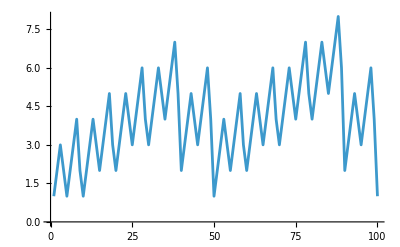

```mathematica
ListLinePlot[StringLength[RomanNumeral[Range[100]]],PlotRange->All]
```

### Exercises from EIWL3 Section 21

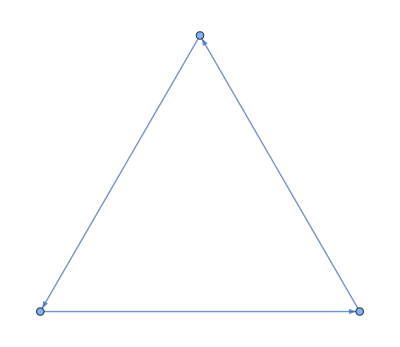

```mathematica
Graph[{1->2,2->3,3->1}]
```

```mathematica
Graph[Flatten[Table[i->j,{i,4},{j,4}]]]
```

-Graphics-

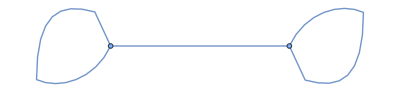
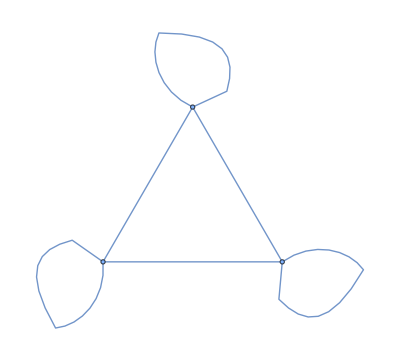
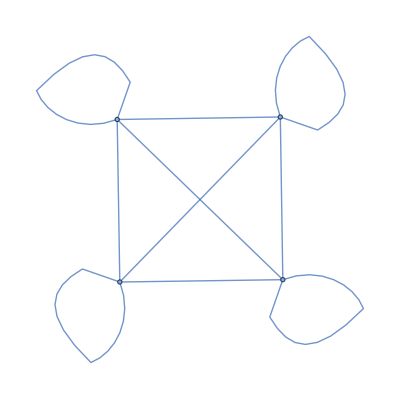
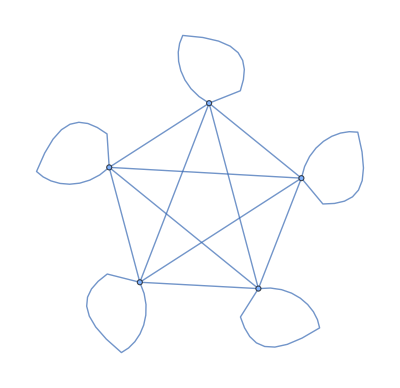
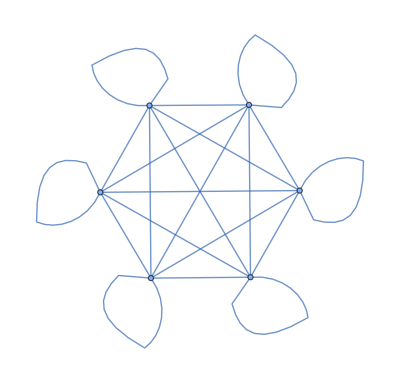
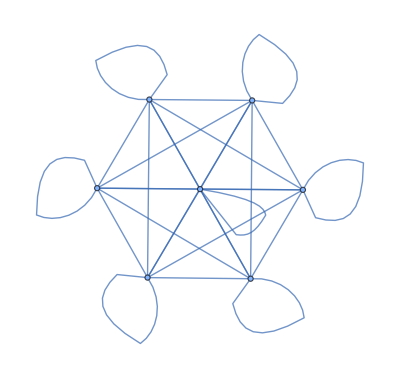
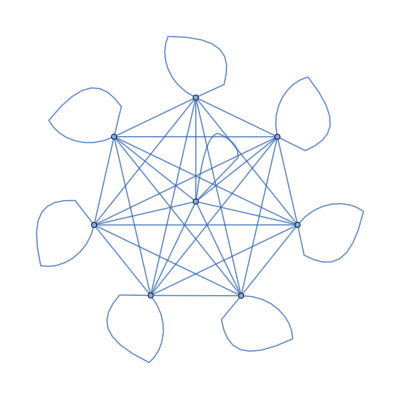
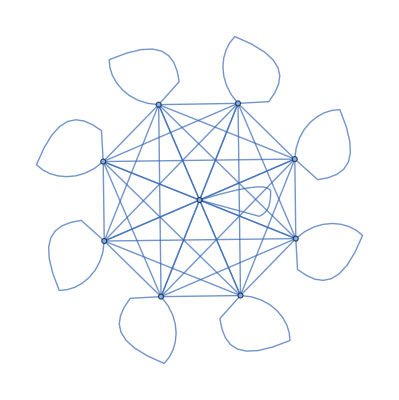

```mathematica
Table[UndirectedGraph[Flatten[Table[i->j,{i,n},{j,n}]]],{n,2,10,1}]
```

```mathematica
Flatten[Table[{1,2},3]]
```

{1,2,1,2,1,2}

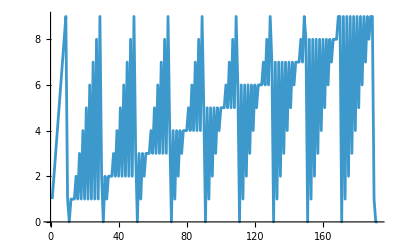

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[100]]]]
```

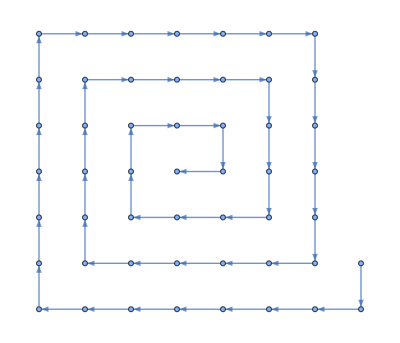

```mathematica
Graph[Table[i->i+1,{i,50}]]
```

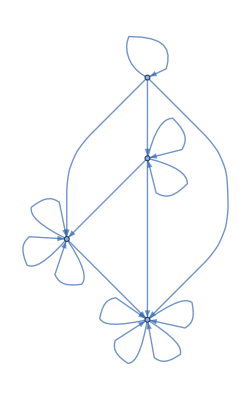

```mathematica
Graph[Flatten[Table[i->Max[i,j],{i,1,4},{j,1,4}]]]
```

```mathematica
Graph[Flatten[Table[i->j-i,{i,5},{j,5}]]]
```

-Graphics-

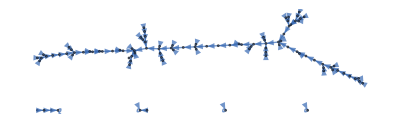

```mathematica
Graph[Flatten[Table[i->RandomInteger[100],{i,100}]]]
```

```mathematica
Graph[Flatten[Table[Table[i->RandomInteger[100],2],{i,100}]]]
```

-Graphics-

```mathematica
Grid[Table[FindShortestPath[{1->2,2->3,3->4,4->1,3->1,2->2},i,j],{i,4},{j,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

### Exercises from EIWL3 Section 20

```mathematica
LanguageIdentify["ajatella"]
```

Finnish

```mathematica
ImageIdentify[Entity["TaxonomicSpecies","PantheraTigris::63rj9"]["Image"]]
```

tiger

```mathematica
Table[ImageIdentify[Blur[Entity["TaxonomicSpecies","PantheraTigris::63rj9"]["Image"],r]],{r,1,5}]
```

{tiger,tiger,tiger,tiger,swift fox}

```mathematica
Classify["Sentiment","I'm so happy to be here"]
```

Positive

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
Nearest[Table[RandomInteger[1000],20],100,3]
```

{93,130,68}

```mathematica
Nearest[Table[RandomColor[],10],Red,5]
```

{RGBColor[0.6225319258508959, 0.18593306565979528, 0.2094404489623325],RGBColor[0.5512702163329348, 0.03190354989300892, 0.16859366253480346],RGBColor[0.6297688758435125, 0.4443266083978423, 0.39773221745299336],RGBColor[0.6012086520281805, 0.5626255729245644, 0.32159434586835145],RGBColor[0.3793668369656229, 0.44633091238732847, 0.16116228918057196]}

```mathematica
Nearest[(Range[100])^2,2000]
```

{2025}

```mathematica
Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]],Entity["Country","Brazil"][EntityProperty["Country","Flag"]],3]
```

{-Graphics-,-Graphics-,-Graphics-}

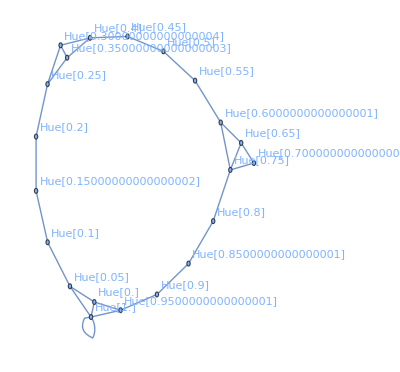

```mathematica
NearestNeighborGraph[Table[Hue[h],{h,0,1,.05}],2, VertexLabels->Automatic]
```

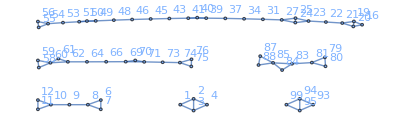

```mathematica
NearestNeighborGraph[Table[RandomInteger[100],100],2,VertexLabels->Automatic]
```


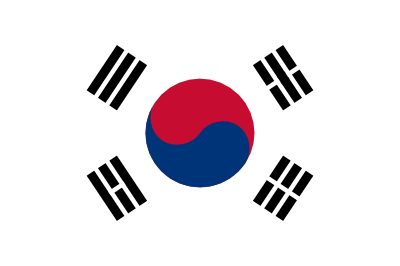
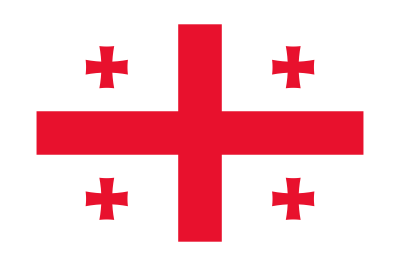
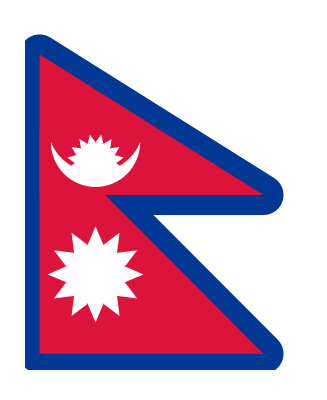
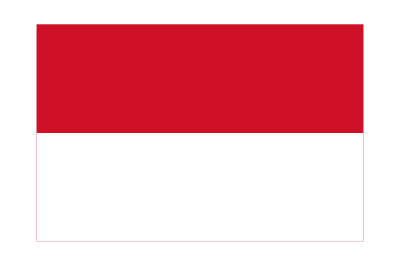
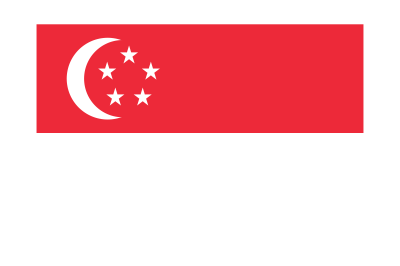
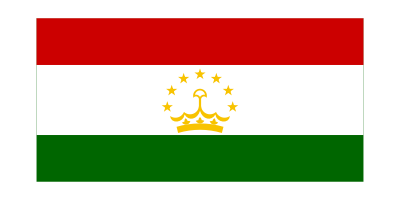
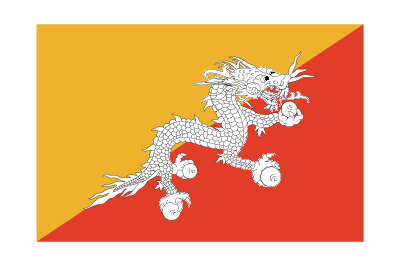
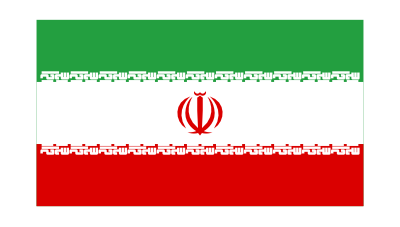

{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
FindClusters[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]]
```

```mathematica
NearestNeighborGraph[Table[Rasterize[FromLetterNumber[n],RasterSize->20],{n,26}],2,VertexLabels->Automatic]
```

-Graphics-

```mathematica
Table[TextRecognize[EdgeDetect[Rasterize["programming",RasterSize->n]]],{n,10,20,1}]
```

{,,,,,,,,,,}

```mathematica
Dendrogram[Table[Rasterize[FromLetterNumber[n]],{n,10}]]
```

-Graphics-

```mathematica
FeatureSpacePlot[Table[Rasterize[ToUpperCase[FromLetterNumber[n]]],{n,26}]]
```

-Graphics-